```mathematica
SetDirectory@NotebookDirectory[]
```

/home/matt/datadrop/Dropbox/Berman-Research/cluster/diss/calcs

```mathematica
dped="../../../defense-prep/eqns/";
dpfd="../../../defense-prep/figs/";
```

```mathematica
{#//Length,#//Last//N,Tan[#[[1;;10]]]//N,Tan[#[[-20;;-1]]]//N}&@Table[s,{s,0,Pi/2,10^-5}]
```

{157080,1.57079,{0.,0.00001,0.00002,0.00003,0.00004,0.00005,0.00006,0.00007,0.00008,0.00009},{5093.55,5366.91,5671.29,6012.26,6396.86,6834.02,7335.32,7915.98,8596.47,9404.97,10381.3,11583.9,13101.6,15076.9,17753.5,21585.8,27527.9,37984.1,61249.,158058.}}

General::munfl: Exp[-2311.54] is too small to represent as a normalized machine number; precision may be lost.

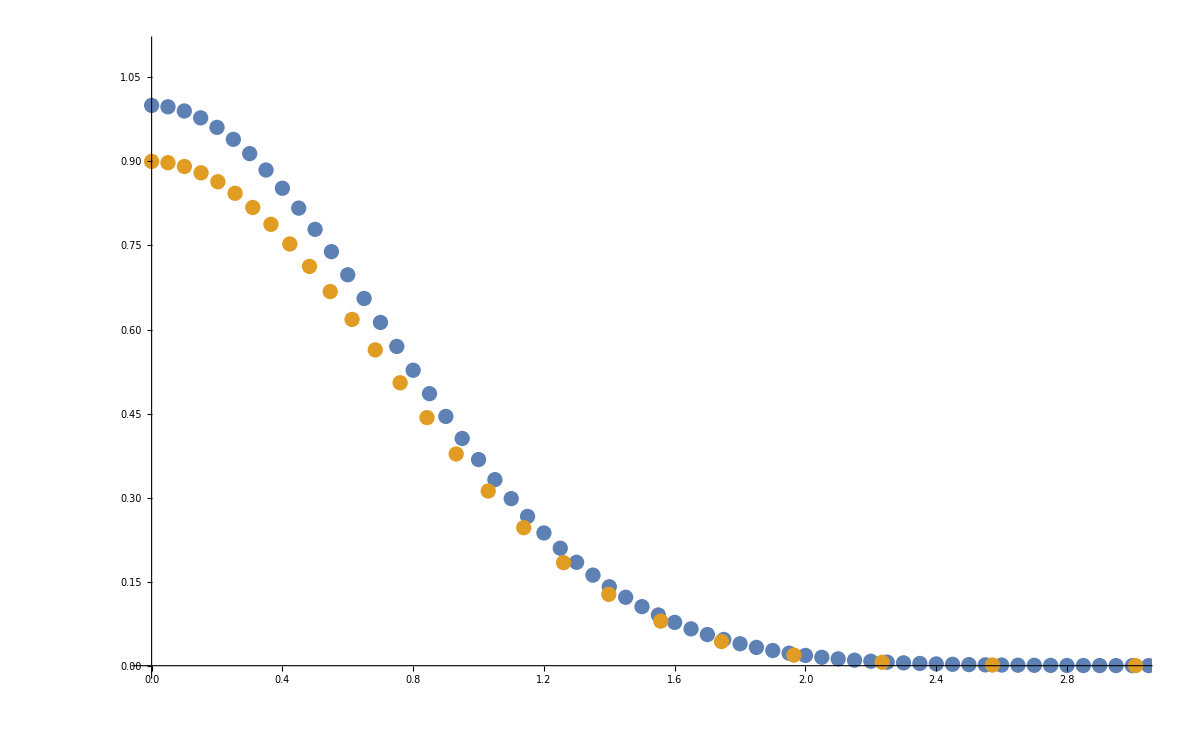

```mathematica
With[
{
f=Function[{x},Exp[-(x^2)]],
ds=(Pi/2)/100
},
ListPlot[
{
Table[
{x,f[x]},
{x,0,10,0.05}
],
Table[
{Tan[s],0.9*f[Tan[s]]},
{s,0,Pi/2,0.05}
]
},
PlotRange->{{0,3},{0,1.1}},
ImageSize->{1200,800}
]]
```

```mathematica
Table[x,{x,0,10^5,1}]//Length
```

100001

```mathematica
({
#//Length,
TableForm@Transpose@{
Tan[#[[1;;20]]]//N,
Tan[#[[(5*10^4)-10;;(5*10^4)+9]]]//N,
Tan[#[[-21;;-2]]]//N
}
})&@Table[s,{s,0,Pi/2,(Pi/2)/(10^5)}]
```

{100001,0. | 0.999654 | 3183.1
0.000015708 | 0.999686 | 3350.63
0.0000314159 | 0.999717 | 3536.78
0.0000471239 | 0.999749 | 3744.82
0.0000628319 | 0.99978 | 3978.87
0.0000785398 | 0.999812 | 4244.13
0.0000942478 | 0.999843 | 4547.28
0.000109956 | 0.999874 | 4897.08
0.000125664 | 0.999906 | 5305.16
0.000141372 | 0.999937 | 5787.45
0.00015708 | 0.999969 | 6366.2
0.000172788 | 1. | 7073.55
0.000188496 | 1.00003 | 7957.75
0.000204204 | 1.00006 | 9094.57
0.000219911 | 1.00009 | 10610.3
0.000235619 | 1.00013 | 12732.4
0.000251327 | 1.00016 | 15915.5
0.000267035 | 1.00019 | 21220.7
0.000282743 | 1.00022 | 31831.
0.000298451 | 1.00025 | 63662.}

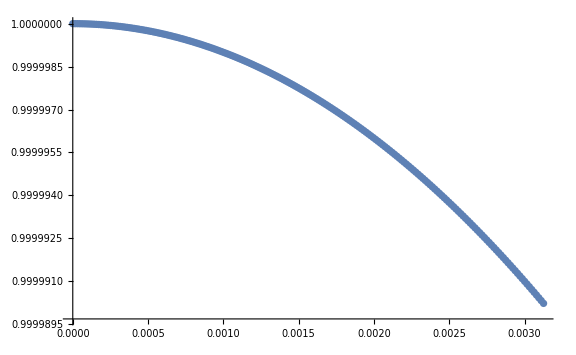
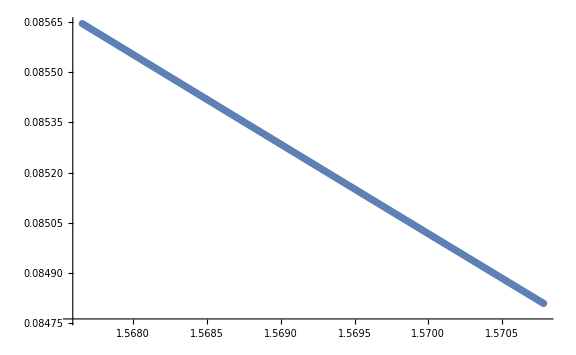

```mathematica
With[
{
pts=Table[s,{s,0,Pi/2,(Pi/2)/(10^5)}],
lpopts={ImageSize->Large,PlotRange->Full}
},
{
ListPlot[Map[{#,Exp[-(#^2)]}&,pts[[;;200]]],Evaluate@FilterRules[{lpopts},Options[ListPlot]]],ListPlot[Map[{#,Exp[-(#^2)]}&,pts[[-201;;-2]]],Evaluate@FilterRules[{lpopts},Options[ListPlot]]]
}
]
```

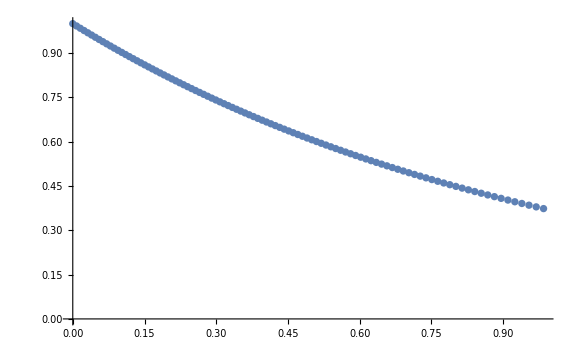
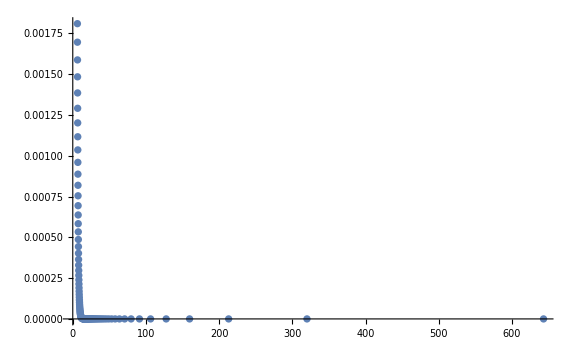

```mathematica
Block[
{
pts=Table[s,{s,0,Pi/2,(Pi/2)/(10^5)}],
lpopts={ImageSize->Large,PlotRange->Full}
},
Map[
ListPlot[
Map[
{
Tan[#],
Exp[-(Tan[#])]
}&,
#],
Evaluate@FilterRules[{lpopts},Options[ListPlot]]
]&,
{pts[[1;;5*10^4;;500]],pts[[2.5*10^4;;7.5*1]],pts[[-10^4;;-2;;100]]}
]
]
```